Initial setup of a simple model of respiration. This model has 3 processes -- oxidation, reduction and anabolism -- a minimum maintenance energy, but no homeostasis reactions. We assume that cell density ρ ≈ 1 g/ml = 1100 g/L, is a constant as is f_C=M_C/M. 

Our convention is to write reactions transforming organic molecules per C atom. Fluxes for those processes, e.g. anabolism, are in units of mol C / biomass / time. Since the molar mass of carbon m_C=12 g/mol we conclude that λ = m_C J_ana. 

First we set up reaction stoichiometries for a respiratory metabolism in matrix form. Then we compute mass balances for the two internal metabolites: A = ATP  and N = NADH. By assuming steady state (time derivatives equal 0) for these metabolites, we then solve for the steady-state growth rate λ as a function of the process fluxes J_α.

```mathematica
(* Assumptions: fluxes, concentrations and maintenance energies are non-negative; ZC values are real, i.e. can be negative. See below for assumptions re stoichiometric coefficients. *)
assump = {{ρ,A,N,Subscript[m, C],Subscript[S, 1]}∈PositiveReals,{Subscript[J, red],Subscript[J, ox],Subscript[J, ana],Subscript[J, h],Subscript[S, 3],Subscript[S, 4],b,Subscript[ϕ, ox],Subscript[ϕ, red],Subscript[ϕ, ana],Subscript[ϕ, O],Subscript[ϕ, H]}∈NonNegativeReals,Subscript[S, 2]∈NegativeReals,{Subscript[Z, C,org],Subscript[Z, C,B],Subscript[Z, C,prod],Subscript[S, 5],Subscript[S, 6]}∈Reals};

(* Symbolic stoichiometric matrix for respiration without homeostasis *)
(* Column order is Subscript[C, red],Subscript[C, ox],Subscript[E, red],Subscript[E, ox],Subscript[EC, red],Subscript[EC, ox],ATP,ADP,biomass *)
(* Row order is oxidation, reduction, anabolism *)
(* oxidation and anabolism written per-C, reduction per-electron. *)
(* Hence fractional stoichiometries for Subscript[E, red] and Subscript[E, ox] on the assumption of 4e- transfer, e.g. O2/H2O *)
(* Note that the fractional stoichs are irrelevant to solutions since we don't balance external metabolites anyway *)
(* Wrote the Subscript[S, i] so that they all contribute positively to ATP and NADH flux balances. *)
(* Subscript[S, 1] = oxidation NADH production (positive value, NADH produced) *)
(* Subscript[S, 2] = reduction NADH production (negative value, NADH consumed) *)
(* Subscript[S, 3] = oxidation ATP production (positive value, ATP produced) *)
(* Subscript[S, 4] = reduction ATP production (positive value, ATP produced) *)
(* Subscript[S, 5] = anabolism ATP production (typically negative, ATP consumed) *)
(* Subscript[S, 6] = anabolism NADH production (negative or positive) *)
SM = {{-1,1,0,0,Subscript[S, 1],-Subscript[S, 1],Subscript[S, 3],-Subscript[S, 3],0},{0,0,0.25,-0.25,Subscript[S, 2],-Subscript[S, 2],Subscript[S, 4],-Subscript[S, 4],0},{-1, 0, 0, 0,Subscript[S, 6],-Subscript[S, 6],Subscript[S, 5],-Subscript[S, 5],1}};
MatrixRank[SM]

(* Matrix with additional homeostasis process -- last row *) 
SMH = {{-1,1,0,0,Subscript[S, 1],-Subscript[S, 1],Subscript[S, 3],-Subscript[S, 3],0},{0,0,0.25,-0.25,Subscript[S, 2],-Subscript[S, 2],Subscript[S, 4],-Subscript[S, 4],0},{-1, 0, 0, 0,Subscript[S, 6],-Subscript[S, 6],Subscript[S, 5],-Subscript[S, 5],1},{0, 0, 0, 0,0,0,-1,1,0}};
(* Notice that the matrix now has rank 4 instead of 3 above -- one more free variable due to the additional reaction *)
MatrixRank[SMH]

JvecH={{Subscript[J, ox]},{Subscript[J, red]},{Subscript[J, ana]}, {Subscript[J, H]}};
massBalances = Dot[Dot[Transpose[SMH], JvecH]];
massBalances//MatrixForm
lambdaSub = {Subscript[J, ana]-> λ/Subscript[m, C]};
dndtH =  massBalances[[5]]-λ*N/.lambdaSub
dadtH = massBalances[[7]]-λ*A-b/.lambdaSub

(* Rate laws for a 0-order system *)
rateLawsZeroOrder = {Subscript[J, ox]-> Subscript[γ, ox]*Subscript[ϕ, ox],Subscript[J, red]-> Subscript[γ, red]*Subscript[ϕ, red],Subscript[J, H]-> Subscript[γ, H]*Subscript[ϕ, H],Subscript[J, ana]-> Subscript[γ, ana]*Subscript[ϕ, ana] };
dndtZOH = dndtH/.rateLawsZeroOrder
dadtZOH = dadtH /.rateLawsZeroOrder 

(* Solve for lambda as f(J) *)
λ/.FullSimplify[Solve[dndtH==0&&dadtH==0, {Subscript[J, red],λ}],assump]
```

3

4

(-J_ana-J_ox
J_ox
0.25 J_red
-0.25 J_red
J_ox S_1+J_red S_2+J_ana S_6
-J_ox S_1-J_red S_2-J_ana S_6
-J_H+J_ox S_3+J_red S_4+J_ana S_5
J_H-J_ox S_3-J_red S_4-J_ana S_5
J_ana)

{-N λ+J_ox S_1+J_red S_2+(λ S_6)/m_C}

{-b-A λ-J_H+J_ox S_3+J_red S_4+(λ S_5)/m_C}

{-N λ+(λ S_6)/m_C+S_1 γ_ox ϕ_ox+S_2 γ_red ϕ_red}

{-b-A λ+(λ S_5)/m_C-γ_H ϕ_H+S_3 γ_ox ϕ_ox+S_4 γ_red ϕ_red}

{-(m_C (S_2 (b+J_H-J_ox S_3)+J_ox S_1 S_4))/(m_C (A S_2-N S_4)-S_2 S_5+S_4 S_6)}

So steady-state λ can be expressed as a function of two process fluxes and two concentrations. If we write a model without the capacity for ATP flux homeostasis (J_H) then the solution will depend on only one process flux. Given some rate law, i.e. functional relationship between fluxes J_α and concentrations of substrate, product and catalyst (ϕ_i, we can derive expressions for λ that depend on those same concentrations.

Here we assume zero-order rate laws, i.e. concentration-independent expressions for J_α, to solve the mass balances above in steady state. Analytic solutions are possible with more realistic rate laws, e.g. Michaelis-Menten approaches, but they are very complex. Zero order rate laws have the form J_α =γ_α ϕ_α where γ_α is a mass-specific kinetic constant and ϕ_α is a mass-fraction. Once we have expressions for mass balances in terms of ϕ_α we can also enforce an allocation constraint Σ ϕ_α = 1, i.e. that the total mass is accounted for.

```mathematica
(* Now solve for lambda as f(phis,gammas) - using mass balances with rate laws substituted in *)
(* Also apply constraint on the Sum(phis)=1 *)
phis = {Subscript[ϕ, ox],Subscript[ϕ, red],Subscript[ϕ, ana],Subscript[ϕ, H],Subscript[ϕ, O]};
phiConst = Total[phis]-1 /.{Subscript[ϕ, ana]-> λ/(Subscript[m, C]*Subscript[γ, ana])};

ZCrelations = {Subscript[S, 1]-> (Subscript[Z, C,ox]-Subscript[Z, C,red])/2, Subscript[S, 6]-> (Subscript[Z, C,B]-Subscript[Z, C,red])/2};
Jsubs = {Subscript[γ, ox] Subscript[ϕ, ox]-> Subscript[J, ox],Subscript[γ, red] Subscript[ϕ, red]->Subscript[J, red],Subscript[γ, ana] Subscript[ϕ, ana]->Subscript[J, ana],Subscript[J, ana]->λ/Subscript[m, C] };

(* Solve analytically for steady-states obeying the constraints as a function of phis *)
solns = FullSimplify[Solve[dndtZOH==0&&dadtZOH==0 &&phiConst==0,{λ,Subscript[ϕ, ox],Subscript[ϕ, red]}], assump]/.Jsubs/.ZCrelations;

(* Getting only λ expression. *)
solns[[1]][[1]]
```

λ→-(m_C γ_ana (S_2 γ_red (b+γ_H ϕ_H+S_3 γ_ox (-1+ϕ_H+ϕ_O))-1/2 γ_ox (b+γ_H ϕ_H+S_4 γ_red (-1+ϕ_H+ϕ_O)) (Z_(C,ox)-Z_(C,red))))/(-(((A m_C-S_5) γ_ana+S_4 γ_red) (-S_2 γ_red+1/2 γ_ox (Z_(C,ox)-Z_(C,red))))+(S_3 γ_ox-S_4 γ_red) (S_2 γ_red+γ_ana (N m_C+1/2 (-Z_(C,B)+Z_(C,red)))))

This is an equation for λ which satisfies all constraints but isn’t optimal. We will use this to calculate how λ depends on Z_(C,B)and Z_(C,red).

We know that at the optimum, Z_(C,B) satisfies the following equation of a line with the following slope K_Z and intercept Z_0.

```mathematica
ZCBexp=1/(Subscript[J, ana] Subscript[γ, ana] (Subscript[S, 3] Subscript[γ, ox]-Subscript[S, 4] Subscript[γ, red]))(Subscript[γ, ana] (2 Subscript[S, 2] Subscript[γ, red] (b+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 3] Subscript[γ, ox] (-1+Subscript[ϕ, H]+Subscript[ϕ, O]))+Subscript[γ, ox] (b+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 4] Subscript[γ, red] (-1+Subscript[ϕ, H]+Subscript[ϕ, O])) (-Subscript[Z, C,ox]+Subscript[Z, C,red]))+Subscript[J, ana] (2 Subscript[S, 2] (-Subscript[S, 5] Subscript[γ, ana]+Subscript[S, 3] Subscript[γ, ox]) Subscript[γ, red]+Subscript[γ, ox] (Subscript[S, 5] Subscript[γ, ana]-Subscript[S, 4] Subscript[γ, red]) Subscript[Z, C,ox]+((Subscript[S, 3]-Subscript[S, 5]) Subscript[γ, ana] Subscript[γ, ox]+Subscript[S, 4] (-Subscript[γ, ana]+Subscript[γ, ox]) Subscript[γ, red]) Subscript[Z, C,red]+Subscript[m, C] Subscript[γ, ana] (2 N Subscript[S, 3] Subscript[γ, ox]+2 A Subscript[S, 2] Subscript[γ, red]-2 N Subscript[S, 4] Subscript[γ, red]+A Subscript[γ, ox] (-Subscript[Z, C,ox]+Subscript[Z, C,red]))))
```

1/(J_ana γ_ana (S_3 γ_ox-S_4 γ_red))(γ_ana (2 S_2 γ_red (b+γ_H ϕ_H+S_3 γ_ox (-1+ϕ_H+ϕ_O))+γ_ox (b+γ_H ϕ_H+S_4 γ_red (-1+ϕ_H+ϕ_O)) (-Z_(C,ox)+Z_(C,red)))+J_ana (2 S_2 (-S_5 γ_ana+S_3 γ_ox) γ_red+γ_ox (S_5 γ_ana-S_4 γ_red) Z_(C,ox)+((S_3-S_5) γ_ana γ_ox+S_4 (-γ_ana+γ_ox) γ_red) Z_(C,red)+m_C γ_ana (2 N S_3 γ_ox+2 A S_2 γ_red-2 N S_4 γ_red+A γ_ox (-Z_(C,ox)+Z_(C,red)))))

```mathematica
Subscript[K, Z]=FullSimplify[D[ZCBexp,Subscript[Z, C,red]]]
Subscript[Z, 0]=FullSimplify[ZCBexp/. Subscript[Z, C,red]->0]
```

(J_ana S_4 γ_ox γ_red+γ_ana (-J_ana S_4 γ_red+γ_ox (b+J_ana (A m_C+S_3-S_5)+γ_H ϕ_H+S_4 γ_red (-1+ϕ_H+ϕ_O))))/(J_ana γ_ana (S_3 γ_ox-S_4 γ_red))

1/(J_ana γ_ana (S_3 γ_ox-S_4 γ_red))(2 (J_ana (S_2 (-S_5 γ_ana+S_3 γ_ox) γ_red+m_C γ_ana (N S_3 γ_ox+(A S_2-N S_4) γ_red))+S_2 γ_ana γ_red (b+γ_H ϕ_H+S_3 γ_ox (-1+ϕ_H+ϕ_O)))-γ_ox (J_ana S_4 γ_red+γ_ana (b+J_ana (A m_C-S_5)+γ_H ϕ_H+S_4 γ_red (-1+ϕ_H+ϕ_O))) Z_(C,ox))

Now to calculate the penalty for deviating from this line, we will go a distance x perpendicular to it. The slope of the perpendicular line will be -1/K_Z.

```mathematica
-1/Subscript[K, Z]
```

-(J_ana γ_ana (S_3 γ_ox-S_4 γ_red))/(J_ana S_4 γ_ox γ_red+γ_ana (-J_ana S_4 γ_red+γ_ox (b+J_ana (A m_C+S_3-S_5)+γ_H ϕ_H+S_4 γ_red (-1+ϕ_H+ϕ_O))))

We need an expression for the growth rate λ along this orthogonal line as a function of x, where x = √[(Z_(C,B)-B_0)^2 + (Z_(C,red)-R_0)^2], and the point (R_0,B_0) is the intersection point of both orthogonal lines. The effect of decreasing λ away from the optimal line should depend only on x, and thus be independent of the intercept of the orthogonal transect. Thus, for simplicity we may choose the point R_0=0, so that the y-intercept B_0 of both lines are identical, i.e., Z_0.

Then to solve for an expression for λ(x), we may  substitute x in the expression for general λ as found above, as well as use a Z_(C,B)that satisfies the equation of the orthogonal line: Z_(C,B)= -1/K_Z Z_(C,red)+ Z_0,

```mathematica
ZCBsubs={Subscript[Z, C,B]-Subscript[Z, C,red]->(-1/Subscript[K, Z]-1)Subscript[Z, C,red]+ Subscript[Z, 0]};
lamSolns = FullSimplify[Solve[dndtZOH==0&&dadtZOH==0 &&phiConst==0,{λ,Subscript[ϕ, ox],Subscript[ϕ, red]}], assump]/.Jsubs/.ZCrelations/.ZCBsubs;
FullSimplify[lamSolns[[1]][[1]]]
```

λ→-(m_C γ_ana (S_2 γ_red (b+γ_H ϕ_H+S_3 γ_ox (-1+ϕ_H+ϕ_O))-1/2 γ_ox (b+γ_H ϕ_H+S_4 γ_red (-1+ϕ_H+ϕ_O)) (Z_(C,ox)-Z_(C,red))))/((S_3 γ_ox-S_4 γ_red) (S_2 γ_red+1/2 γ_ana (2 N m_C-Z_(C,B)+Z_(C,red)))+1/2 ((A m_C-S_5) γ_ana+S_4 γ_red) (2 S_2 γ_red+γ_ox (-Z_(C,ox)+Z_(C,red))))

```mathematica
lamFinExp = -((Subscript[m, C] Subscript[γ, ana] (Subscript[S, 2] Subscript[γ, red] (b+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 3] Subscript[γ, ox] (-1+Subscript[ϕ, H]+Subscript[ϕ, O]))-1/2 Subscript[γ, ox] (b+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 4] Subscript[γ, red] (-1+Subscript[ϕ, H]+Subscript[ϕ, O])) (Subscript[Z, C,ox]-Subscript[Z, C,red])))/(1/2 ((A Subscript[m, C]-Subscript[S, 5]) Subscript[γ, ana]+Subscript[S, 4] Subscript[γ, red]) (2 Subscript[S, 2] Subscript[γ, red]+Subscript[γ, ox] (-Subscript[Z, C,ox]+Subscript[Z, C,red]))+(Subscript[S, 3] Subscript[γ, ox]-Subscript[S, 4] Subscript[γ, red]) (Subscript[S, 2] Subscript[γ, red]+1/2 Subscript[γ, ana] (Subscript[Z, C,red]+1/(Subscript[S, 3] Subscript[γ, ox]-Subscript[S, 4] Subscript[γ, red])((-2 Subscript[S, 2] ((A Subscript[m, C]-Subscript[S, 5]) Subscript[γ, ana]+Subscript[S, 3] Subscript[γ, ox]) Subscript[γ, red]+Subscript[γ, ox] ((A Subscript[m, C]-Subscript[S, 5]) Subscript[γ, ana]+Subscript[S, 4] Subscript[γ, red]) Subscript[Z, C,ox])/Subscript[γ, ana]+(-2 Subscript[S, 2] Subscript[γ, red] (b+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 3] Subscript[γ, ox] (-1+Subscript[ϕ, H]+Subscript[ϕ, O]))+Subscript[γ, ox] (b+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 4] Subscript[γ, red] (-1+Subscript[ϕ, H]+Subscript[ϕ, O])) Subscript[Z, C,ox])/Subscript[J, ana]+(Subscript[J, ana] Subscript[γ, ana] (Subscript[S, 3] Subscript[γ, ox]-Subscript[S, 4] Subscript[γ, red])^2 Subscript[Z, C,red])/(Subscript[J, ana] Subscript[S, 4] Subscript[γ, ox] Subscript[γ, red]+Subscript[γ, ana] (-Subscript[J, ana] Subscript[S, 4] Subscript[γ, red]+Subscript[γ, ox] (b+Subscript[J, ana] (A Subscript[m, C]+Subscript[S, 3]-Subscript[S, 5])+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 4] Subscript[γ, red] (-1+Subscript[ϕ, H]+Subscript[ϕ, O])))))))));
FullSimplify[D[lamFinExp,Subscript[Z, C,B]]]
```

0

# Numerical evaluation of λ(x)

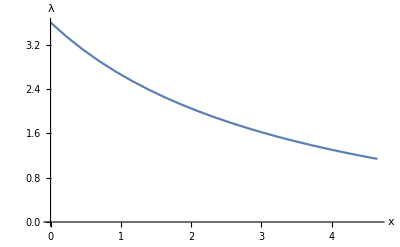

```mathematica
(*Define parameters*)
params={A->10^-7,
N->10^-7,
b->0.1,
Subscript[γ, H]->0.5,
Subscript[γ, ana]->0.5,
Subscript[γ, ox]->0.5,
Subscript[γ, red]->0.5,
Subscript[m, C]->12,
Subscript[J, ana]->0.3,
Subscript[ϕ, H]->0.1,
Subscript[ϕ, O]->0.4,
Subscript[S, 2]->2,
Subscript[S, 3]->0.3,
Subscript[S, 4]->1,
Subscript[S, 5]->0.3,
Subscript[Z, C,ox]->4};

Subscript[Z, 0]->1/(Subscript[J, ana] Subscript[γ, ana] (Subscript[S, 3] Subscript[γ, ox]-Subscript[S, 4] Subscript[γ, red]))(2 (Subscript[J, ana] (Subscript[S, 2] (-Subscript[S, 5] Subscript[γ, ana]+Subscript[S, 3] Subscript[γ, ox]) Subscript[γ, red]+Subscript[m, C] Subscript[γ, ana] (N Subscript[S, 3] Subscript[γ, ox]+(A Subscript[S, 2]-N Subscript[S, 4]) Subscript[γ, red]))+Subscript[S, 2] Subscript[γ, ana] Subscript[γ, red] (b+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 3] Subscript[γ, ox] (-1+Subscript[ϕ, H]+Subscript[ϕ, O])))-Subscript[γ, ox] (Subscript[J, ana] Subscript[S, 4] Subscript[γ, red]+Subscript[γ, ana] (b+Subscript[J, ana] (A Subscript[m, C]-Subscript[S, 5])+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 4] Subscript[γ, red] (-1+Subscript[ϕ, H]+Subscript[ϕ, O]))) Subscript[Z, C,ox])/.params;

Subscript[K, Z]->(Subscript[J, ana] Subscript[S, 4] Subscript[γ, ox] Subscript[γ, red]+Subscript[γ, ana] (-Subscript[J, ana] Subscript[S, 4] Subscript[γ, red]+Subscript[γ, ox] (b+Subscript[J, ana] (A Subscript[m, C]+Subscript[S, 3]-Subscript[S, 5])+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 4] Subscript[γ, red] (-1+Subscript[ϕ, H]+Subscript[ϕ, O]))))/(Subscript[J, ana] Subscript[γ, ana] (Subscript[S, 3] Subscript[γ, ox]-Subscript[S, 4] Subscript[γ, red]))/.params;

(*Define a function for Z_C,B*)
Subscript[Z, C,B][ZCred_]:=((-1/Subscript[K, Z])ZCred+ Subscript[Z, 0])/.params;
(*Define the distance x*)
x[ZCB_,ZCred_]:=Sqrt[(ZCB-Subscript[Z, 0])^2+(ZCred)^2]/.params;

(*Define λ as a function of Subscript[Z, C] variables*)
λ[ZCB_,ZCred_]:=-(Subscript[m, C] Subscript[γ, ana] (Subscript[S, 2] Subscript[γ, red] (b+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 3] Subscript[γ, ox] (-1+Subscript[ϕ, H]+Subscript[ϕ, O]))-1/2 Subscript[γ, ox] (b+Subscript[γ, H] Subscript[ϕ, H]+Subscript[S, 4] Subscript[γ, red] (-1+Subscript[ϕ, H]+Subscript[ϕ, O])) (Subscript[Z, C,ox]-ZCred)))/(-(((A Subscript[m, C]-Subscript[S, 5]) Subscript[γ, ana]+Subscript[S, 4] Subscript[γ, red]) (-Subscript[S, 2] Subscript[γ, red]+1/2 Subscript[γ, ox] (Subscript[Z, C,ox]-ZCred)))+(Subscript[S, 3] Subscript[γ, ox]-Subscript[S, 4] Subscript[γ, red]) (Subscript[S, 2] Subscript[γ, red]+Subscript[γ, ana] (N Subscript[m, C]+1/2 (-ZCB+ZCred))))/.params;

(*Create a table of values for λ and x*)
data=Table[{xValue=x[Subscript[Z, C,B][ZCred],ZCred]/.params,lambdaValue=λ[Subscript[Z, C,B][ZCred],ZCred]/.params},{ZCred,0,2,0.1} ]/.params;

(*Step 7:Plot Lambda as a function of x*)
ListPlot[data,Joined->True,AxesLabel->{"x","λ"}]
```

```mathematica
data
```

{{0.,3.6},{0.232595,3.33826},{0.465189,3.10581},{0.697784,2.89799},{0.930379,2.71109},{1.16297,2.54209},{1.39557,2.38855},{1.62816,2.24844},{1.86076,2.12006},{2.09335,2.002},{2.32595,1.89307},{2.55854,1.79225},{2.79114,1.69866},{3.02373,1.61156},{3.25633,1.53028},{3.48892,1.45428},{3.72152,1.38304},{3.95411,1.31613},{4.18671,1.25318},{4.4193,1.19383},{4.65189,1.1378}}

3.51971-0.904712 x+0.0869147 x^2

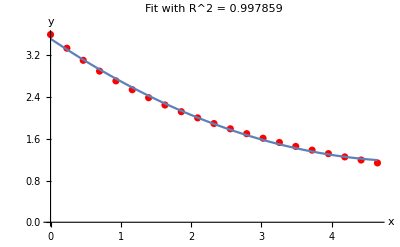

```mathematica
fittedModel=Fit[data,{1,x, x^2},x]

(*Calculating R^2*)
yActual=data[[All,2]];
yPredicted=fittedModel/. x->data[[All,1]];
totalSS=Total[(yActual-Mean[yActual])^2];
residualSS=Total[(yActual-yPredicted)^2];
rSquared=1-residualSS/totalSS;

(*Plotting for visual inspection*)
Show[ListPlot[data,PlotStyle->Red],Plot[fittedModel,{x,Min[data[[All,1]]],Max[data[[All,1]]]}],PlotLabel->"Fit with R^2 = "<>ToString[rSquared],AxesLabel->{"x","y"}]
```

3.22191-0.500394 x

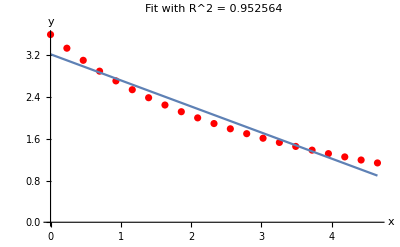

```mathematica
fittedModel=Fit[data,{1,x},x]

(*Calculating R^2*)
yActual=data[[All,2]];
yPredicted=fittedModel/. x->data[[All,1]];
totalSS=Total[(yActual-Mean[yActual])^2];
residualSS=Total[(yActual-yPredicted)^2];
rSquared=1-residualSS/totalSS;

(*Plotting for visual inspection*)
Show[ListPlot[data,PlotStyle->Red],Plot[fittedModel,{x,Min[data[[All,1]]],Max[data[[All,1]]]}],PlotLabel->"Fit with R^2 = "<>ToString[rSquared],AxesLabel->{"x","y"}]
```